## Quantization of the Electromagnetic field

See also Knight and Allen in library reserves, Ch 14 Townsend

∇·𝔼=0 	∇×𝔼=-1/c(∂𝔹)/(∂t)   ∇·𝔹=0 	∇×𝔹=1/c(∂𝔼)/(∂t)

single mode 𝔼=x̂ ℰ(t) cos[k z],𝔹 = ŷ ℬ (t) sin[k z]
curl equations: ω ℰ=ℬ̇   , -ω ℬ=ℰ̇  
-∂_z 𝔹_y=1/c ℰ̇ cos[k z]→𝔹=-ŷ (ℰ̇)/ω sin[k z]

Hamiltonian  	H =1/(8π)∫ⅆV (𝔼·𝔼+𝔹·𝔹)=1/(8π)∫ⅆV (ℰ^2/2+(ℰ̇)^2/(2 ω^2))=V/(8π ω^2)(1/2 ω^2 ℰ^2+1/2(ℰ̇)^2) =1/2(ω^2 q^2+p^2)

Hamilton’s equations 	  ṗ=-(∂H)/(∂ q), q̇=(∂H)/(∂ p)→ q=√(V/(8π ω^2))ℰ, p=√(V/(8π ω^2))ℰ̇=-√(V/(8π))ℬ

“Canonical quantization”: once you know the classical coordinate and conjugate momentum operators, replace p→ p̂, q→ q̂, and quantize using [q̂,p̂]=ⅈ ℏ.

[q,p]=ⅈ ℏ, let   a=√(1/(2ℏ ω))( ω q+ⅈ p), a^†=√(1/(2ℏ ω))(ω q-ⅈ p), [a,a^†]=1/(2ℏ ω)[ω q,-ⅈ p]+1/(2ℏ)[ⅈ p,q]=1
p^2+ω^2 q^2=ℏ ω ((a-a^†)/(√2 ⅈ))^2+ω^2 ℏ/ω ((a+a^†)/(√2))^2=ℏω( a a^†+a a^†)=(2 N̂+1)ℏω→ H=ℏω (N̂+1/2)

So electromagnetic field mode has identical properties to a simple harmonic oscillator:  𝒩̂ n=(â)^†an=nn, n=0,1,2,...  The energies are Hn=ℏω(n+1/2)n.  n=((a^†)^n)/(√(n!))0

Electric field operator ℰ=√((8π ω^2)/V)q=√((4π ℏ ω)/V)(a+a^†)=ℰ_1(a+a^†)
Magnetic field ℬ=-√((8π)/V)p=ⅈ ℰ_1(a-a^†)

```mathematica
Solve[{a==√(1/(2ℏ ω))( ω q+ⅈ p), a†==√(1/(2ℏ ω))(ω q-ⅈ p)},{p,q}]//Simplify//PowerExpand
```

{{p→-(ⅈ (a-a†) √ω √ℏ)/(√2),q→((a+a†) √ℏ)/(√2 √ω)}}

```mathematica
({ℰ,ℬ}/.{ℰ-> √((8π ω^2)/V)q,ℬ-> -√((8π)/V)p}/.%)//Simplify//PowerExpand
```

{{(2 (a+a†) √π √ω √ℏ)/(√V),(2 ⅈ (a-a†) √π √ω √ℏ)/(√V)}}

Key point:  The electric and magnetic field operators are time-independent.

```mathematica
[ℰ,ℬ]=ⅈ (Subscript[ℰ, 1]^2)[a+SuperDagger[a],a-SuperDagger[a]]=-2ⅈ (Subscript[ℰ, 1]^2)[a,SuperDagger[a]]=-2ⅈ Subscript[ℰ, 1]^2 -> Δℰ Δℬ≥Subscript[ℰ, 1]^2
```

nℰn=ℰ_1 n(a+a^†)n=0 but n ℰ^2 n=ℰ_1^2(n(a+a^†))^2 n=ℰ_1^2 na a^†+a^†an=ℰ_1^2 n2 a^†a+1n=(2n+1)ℰ_1^2

so the electric field has zero average value but contributes 1/2 the energy

[N̂,ℰ]=ℰ_1[N,(a+a^†)]=ℰ_1(a^†-a)=-ⅈ ℬ→ Δℰ ΔN≥ 1/2|[ℰ,N]|=1/2|⟨ℬ⟩|

so we need a superposition of n states to have a non-zero mean field

ψ=1/(√2)n+1/(√2)n+1ⅇ^(ⅈ δ): ψℰψ=1/2 nℰn+1 ⅇ^(ⅈ δ)+1/2 n+1ℰn ⅇ^(-ⅈ δ)=ℰ_1 √(n+1)cos[δ]

### Interaction of an atom with a single quantized field mode

The classical Hamiltonian for an electron (charge -e)  interacting with an applied electromagnetic field with scalar and vector potentials φ, A is

H=m/2 v^2+V(r)-e φ+H_field=1/(2m)(p+(e A)/c)^2+V(r)-e φ+H_field

where the canonical momentum is p=m x^·-(e A)/c.  Our mode has φ=0, A=𝒜 x̂ cos[k z].  Let’s check that our electron in this mode obeys the classical Lorentz force:

(ṗ)_z=m ż -e/c (Ȧ)_z=m ż = -∂_z H =- 1/m (m v)·(e/c ∂_z A) - ∂_z V =-e/c v_x B_y- ∂_z V=-e/c(v×B)_z- ∂_z V ✓
(ṗ)_x=m ẋ -e/c (Ȧ)_x=m  ẋ +(e E_x+e v_z/c∂_z A_x)=m  ẋ -e E_x+e v_z/c B_y=- ∂_x V→ m ẋ=- ∂_x V-e E_x-e/c(v ×B)_x✓
(ṗ)_y=m ẏ -e/c (Ȧ)_y=m  ẏ =m  ẏ =- ∂_y V→ m ẏ=- ∂_y V✓
so this choice of the Hamiltonian and canonical momentum correctly reproduces the Lorentz force.  The transition to quantum mechanics is the familiar [x,p_x]=ⅈ ℏ so the momentum operator is p_x=-ⅈ ℏ ∂_x (similar for y and z).

We want to write the Hamiltonian in terms of the electric field instead of the vector potential.  Let’s make a unitary transformation of the Hamiltonian, with U=ⅇ^(-ⅈ x (e A_x(t))/(ℏ c)).  Now, assuming we can ignore gradients of A, (p+(e A)/c) U=U(p+(e A)/c)-ⅈ ℏ (∇U)=U(p+(e A)/c)-ⅈ ℏ U (-ⅈ  (e A_x)/(ℏ c))=U p
and
ⅈ ℏ∂_t U ψ=U ⅈ ℏ∂_t ψ+ⅈ ℏ U ψ (-ⅈ x e/(ℏ c)∂_t A_x)=ⅈ ℏ U ∂_t ψ+U ( - e x E_x)ψ

The Schrodinger equation becomes

ⅈ ℏ ∂_t ψ - e x E_x ψ=U^†H U ψ+H_field=1/(2 m)(U^†(p+(e A)/c))^2 U+V(r)+H_field=1/(2 m)p^2 +V(r)+H_field

H=1/(2 m)p^2 +V(r)+H_field+e x E_x=H^0+e x̂ (Ê)_x

It is important to note that the light-atom interaction, V̂=e x̂ (Ê)_x, is time-independent in the fully quantized approach.  It is a product of an atomic operator x̂, and a time-independent field operator (Ê)_x.  The time-dependence arises from the deBroglie clock evolution of the quantum states, not from any time-dependence of the perturbation.  This is the so-called “Schrodinger picture”.

Our unperturbed eigenstates are products of atomic and field eigenstates:

H^0 k,n=(E_k+(n+1/2)ℏω)k,n

Let us focus on two particular atomic states, with energies E_g and E_k, and assume that the Bohr condition, ℏω≈E_k-E_g, is nearly satisfied.  The lowest energy is g,0 with energy E_g+ℏω/2.  The first excited states come in a pair, with nearly the same energy: g,1, k,0, energies E_g+3/2 ℏω, E_k+ℏω/2.  In fact, the energy ladder of energy levels comes in nearly degenerate pairs g,n and k, n-1 with energies E_g+(n+1/2)ℏω and E_k+(n-1/2)ℏω.

Recognizing the degeneracy, we now only need to consider this problem 2 states at a time.  The matrix elements of V̂ are

g,n V̂ k,n-1=eg x̂ knℰ_1(a+a^†)n-1=e ℰ_1 g x̂ kn a^†n-1=e ℰ_1 g x̂ kn a^†n-1

Note that only the creation operator a^† contributes.  Similarly, k,n-1 V̂ g,n=e ℰ_1 k x̂ gn-1an.   Since the matrix elements  k x̂ g are usually real, we can define atomic raising and lowering operators b=gk, b^†=kg so that x̂=x_kg(b+b^†).  Then we would get exactly the same matrix elements if we rewrote our Hamiltonian as

H=H^0+e x̂ (Ê)_x≈H^0+e ℰ_1 x_kg (b a^†+b^†a)

When the perturbation causes  a photon to be created with the a^†operator, it simultaneously causes the atom to go from the excited state to the gnd state.  When a photon is destroyed (â) the atom is excited (b^†).  These are the two energy conserving processes.  The approximation where the non-conserving parts are ignored is called the rotating wave approximation.

In the 2-state approximation, the rotating wave Hamiltonian is

H = E_g+(n+1/2)ℏω+(0 | √n ℏΩ/2
√n ℏΩ/2 | -ℏΔ)

where the single-photon Rabi frequency is defined by Ω=2 e ℰ_1 x_kg/ℏ and the detuning is Δ=ω-ω_kg=ω-(E_k-E_g)/ℏ. An atom that is initially in the ground state in the presence of a single photon will oscillate back and forth from the ground and excited states at the frequency √(Δ^2+Ω^2)

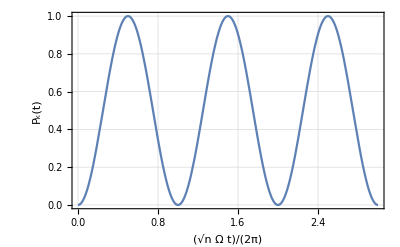

```mathematica
ThadPlot[Abs[{0,1}.MatrixExp[-ⅈ ({{0, √n Ω/2}, {√n Ω/2, -Δ}}/.{Ω->2π,Δ->0,n->1})t].{1,0}]^2,{t,0,3},{},{"(√n Ω t)/(2π)","P_k(t)"}]
```

```mathematica
{1,0}.MatrixExp[-ⅈ ({{0, √n Ω/2}, {√n Ω/2, -Δ}})t].{1,0}//ExpToTrig//Simplify
```

{{((Cos[(t Δ)/2]+ⅈ Sin[(t Δ)/2]) (√(Δ^2+n Ω^2) Cos[1/2 t √(Δ^2+n Ω^2)]-ⅈ Δ Sin[1/2 t √(Δ^2+n Ω^2)]))/(√(Δ^2+n Ω^2))}}

```mathematica
% %^*//Simplify
```

{{(2 Δ^2+n Ω^2+n Ω^2 Cos[t √(Δ^2+n Ω^2)])/(2 Δ^2+2 n Ω^2)}}

### Spontaneous Emission of light

Now let’s let the atom interact with all the modes of the field.  Since it is only changes in energy that can matter, we will from now on measure energy with respect to each mode of the field having n_l=0, thus eliminating the need to constantly worry about the zero-point energy of the field.

First, we need to generalize our field operators.  We take our classical modes to be 𝔼_l=ℰ_l ϵ_l ⅇ^(ⅈ k_l·r). The magnetic field is then found from    ⅈ k_l × 𝔹_l=1/c (ℰ̇)_l ϵ_l ⅇ^(ⅈ k_l·r)  The Hamiltonian for each mode  is  H_l =1/(8π)∫ⅆV (𝔼_l·𝔼_l+𝔹_l·𝔹_l)=1/(8π)∫ⅆV (ℰ_l^2+OverDot[ℰ_l]^2/ω^2)=V/(4π ω^2)(1/2 ω^2 ℰ_l^2+1/2((ℰ̇)_l)^2) =1/2(ω^2 q^2+p^2)  .  We can then continue from the single mode case except the electric field per photon is ℰ_l=√((2π ℏ ω)/V).

In many modern experiments only a small number of modes will have n>0, and the vast majority of the modes are in the vacuum state.  The problem of spontaneous emission addresses what happens to an excited atom in the presence of only vacuum modes.  The initial state of the atom+field is thus e,0, energy E_e, where zero denotes all of the field modes being in the vacuum state.  The e,0 state is nearly degenerate with a large number of states g,1_l, where 1_l denotes the l-th state having 1 photon, all others 0 photons.  These states have energy E_g+ℏω_l.  We expect the states with E_g+ℏω_l≈E_e to be most important for the problem.

We expand the quantum state as ψ=ⅇ^(-ⅈ E_e t/ℏ)(c_e0 e,0+∑_l c_gl g,1_l).  Plugging this into the Schrodinger Eqn, we get for the amplitudes

ⅈ ℏ (ċ)_e0=∑_l (ℏ Ω_l)/2 e,0 b^†a_l g,1_l c_gl
ⅈ ℏ (ċ)_gl=(E_g-E_e+ℏω_l)c_gl+(ℏ Ω_l)/2 g,1_lb a_l^†e,0 c_e0

Since there are lots of modes l, none of them being particularly special, we expect that c_gl<<1.  In addition, the vacuum Rabi frequency Ω_l=(2 e)/ℏ √((2π ℏ ω_l)/V)er·ϵ_lg should be small for large volumes.  We note that when a photon is emitted into a mode, it hits the wall of the box in a time of order L/c that can be many nanoseconds.  Furthermore, when it hits the wall, the wall likely scatters it in some direction (or absorbs it) so it doesn’t return to re-excite the atom.  Thus we should to to the problem an effect “photon lifetime”=1/γ that will keep an emitted photon from returning.  We can accomplish this by adding a term -ⅈ (ℏ γ)/2 c_gl to the (ċ)_gl equation.  Hopefully our final answer does not depend on the assumed value of γ, except that by assuming γ>>Ω_l we are assured that c_gl<<1.

ⅈ ℏ (ċ)_gl=(E_g-E_e+ℏω_l-ⅈ (ℏ Γ)/2)c_gl+(ℏ Ω_l)/2 c_e0→ c_gl≈Ω_l/(2 (ⅈ γ/2+(ω_eg-ω_l)))c_e0

Substituting this into the (ċ)_e0equation gives

ⅈ ℏ (ċ)_e0=∑_l (ℏ Ω_l)/2 c_gl=∑_l ℏ(Ω_l^2/4)/(ⅈ γ/2+(ω_eg-ω_l))c_e0=(δE-ⅈ ℏ Γ/2)c_e0

The coupling of the atoms to the vacuum fields produces a “Lamb shift” in the energies:

δE=∑_l (ℏ Ω_l^2)/4(ω_eg- ω_l)/(γ^2/4+(ω_eg-ω_l)^2)

and causes the excited state to decay via radiation:

Γ=∑_l (γ  Ω_l^2)/(γ^2+4 (ω_eg-ω_l)^2)

There are many cavity modes l whose frequency is close to ω_eg.  The modes, which we take to have the electric field Ê=ℰ_l  ⅇ^(ⅈ k·r) (a+a^†) over our box with  have wavevectors k_l=(2π)/L(m_x,m_y,m_z)=(2π m)/L (sinθ cosϕ,sinθ sinϕ, cosθ), and two polarizations ϵ_1=(cosθ cosϕ,cosθ sinϕ, -sinθ) and  ϵ_2=(-sinϕ,cosϕ,0).     We can therefore write, using ω_l=c k_l=2π m c/L,

Γ=∑_ϵ ∫ⅆ m_xⅆ m_yⅆ m_z(γ  Ω_l^2)/(γ^2+4 (ω_eg-ω_l)^2)=∑_ϵ ((2 e)/ℏ √((2π ℏ)/V))^2∫m^2 ⅆm sinθ ⅆθⅆϕ (ω_l(|er·ϵ_lg|)^2 γ)/(γ^2+4 (ω_eg-ω_l)^2)
=∑_ϵ (4 π e^2)/(ℏ V)(L/(2π c))^3∫sinθ ⅆθⅆϕ(|er·ϵ_lg|)^2∫ω_l^2 ⅆ ω_l  (ω_l γ)/(γ^2+4 (ω_eg-ω_l)^2)

The last integral is done by recognizing that the integrand is strongly peaked at the Bohr condition w=ω_l-ω_eg≈0, so we can pull the factors of ω_l out of the integral: ∫ω_l^2 ⅆ ω_l  (ω_l γ)/(γ^2+4 (ω_eg-ω_l)^2)≈ω_l^3∫_(-∞)^∞ ⅆw γ/(γ^2+4 w^2)=ω_l^3 π/2.  Notice that the γ disappears!  Our result does not depend on the value of the photon lifetime in the cavity.

Γ=(e^2 ω_l^3)/(2 c^3 π  ℏ)∑_ϵ ∫sinθ ⅆθⅆϕ(|er·ϵ_lg|)^2

We are nearly done. Look next at the ϕ integral, and take ϵ=ϵ_2.  (|er·ϵ_2g|)^2=(|ey cosϕ-x sinϕg|)^2=(|ey g|)^2 cos^2 ϕ+(|ex g|)^2 sin^2 ϕ-ey ggx esinϕ cos ϕ-ex ggy esinϕ cos ϕ. When we integrate over ϕ, the cross terms that are proportional to sinϕ cosϕ will be zero.  Thus only the (|ex g|)^2 and (|ey g|)^2 terms contribute.  Thus, if we define ℐ(f)=∫sinθ ⅆθⅆϕ f(θ,ϕ),
the sum is

∑_ϵ ∫sinθ ⅆθⅆϕ(|er·ϵ_lg|)^2=(|ex g|)^2(ℐ(cos^2 ϕ)+ℐ(sin^2 ϕ cos^2 θ))+(|ey g|)^2(ℐ(sin^2 ϕ)+ℐ(cos^2 ϕ cos^2 θ)+(|ezg|)^2 ℐ(sin^2 θ)
=(8π)/3((|ex g|)^2+(|ey g|)^2+(|ez g|)^2)

```mathematica
ℐ[f_]:=Integrate[Sin[th] f,{th,0,π},{ph,0,2π}];xsq (ℐ[Cos[ph]^2]+ℐ[Cos[th]^2 Sin[ph]^2])+ysq(ℐ[Sin[ph]^2]+ℐ[Cos[th]^2 Cos[ph]^2])+zsq ℐ[Sin[th]^2]
```

(8 π xsq)/3+(8 π ysq)/3+(8 π zsq)/3

and the final equation for the spontaneous emission rate is

Γ=(4 e^2  ω_l^3)/(3 c^3 ℏ)(|er g|)^2

THis is the same equation we got for spontaneous emission in our black-body analysis.  Check for Hydrogen 2p→ 1s:

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

```mathematica
(4 e^2  Subscript[ω, l]^3)/(3 c^3  ℏ)rmat^2//.{rmat-> Integrate [Subscript[P, 1,0][r] SphericalHarmonicY[0,0,th,ph]r Cos[th]Subscript[P, 2,1][r] SphericalHarmonicY[1,0,th,ph]Sin[th],{th,0,π},{ph,0,2π},{r,0,∞}]0.5292 Å,Subscript[ω, l]->1/ℏ 13.6eV(1/1^2-1/2^2) ,e^2-> 14.4 eV Å,ℏ-> 1973 eV Å/c,c->3 10^18 Å/sec}
```

(6.26891×10^8)/sec

```mathematica
1/%
```

1.59517×10^-9 sec

which agrees with experiment.

### Scattering of light

We have seen that the interaction of the atom with the vacuum modes of the field can be approximated by adding a term -ⅈ ℏ Γ/2 c_(k n-1) to the excited state amplitude.  We can thus understand the interaction of the atom with an external field with n>>1, by simply adding the spontaneous emission term to the time evolution:

ⅈ ℏ (ċ)_(k n-1)=-ℏ Δ c_(k n-1)+k n-1e z ℰ  ag n c_(g n)-ⅈ ℏ Γ/2 c_(k n-1)=-ℏ ( Δ+ⅈ Γ/2) c_(k n-1)+(ℏ √n Ω)/2 c_(g n)

When the excitation is weak enough, the atom will quickly (time~1/Γ) reach a steady state where the reduction in excited state amplitude due to spontaneous emission is balancing the  production due to the Rabi coupling.  Thus we can solve this equation in steady state to get

0=-ℏ ( Δ+ⅈ Γ/2) c_(k n-1)+(ℏ √n Ω)/2 c_(g n)→c_(k n-1)=(√n Ω)/(2( Δ+ⅈ Γ/2)) .

The rate that the atom emits photons into the other modes is

R=Γ P_(e n-1)=Γ (|c_(e n-1)|)^2=Γ (|(√n Ω)/(2( Δ+ⅈ Γ/2))|)^2=(Γ n Ω^2)/(4 Δ^2+ Γ^2)

We can interpret this equation in terms of scattering:  the scattering rate is the number of photons/sec per unit area times the effective area of the atom.  The number of photons per second is the intensity (energy/sec) divided by the energy per photon:

R=σ I/(ℏ ω)

The intensity of the light is the energy density times the speed of light:

I=c H/V=c(ℏ ω n)/V=c/(8π)⟨E^2⟩

Setting the two rates equal:

R=(Γ n Ω^2)/(4 Δ^2+ Γ^2) =σ I/(ℏ ω)
(Γ n)/(4 Δ^2+ Γ^2)e^2/ℏ^2((2π ℏ ω)/V)=σ (c n)/V → σ=(2 e^2 π  Γ ω)/(ℏ c (Γ^2+4 Δ^2))(|kzg|)^2=σ_0/(1+4 Δ^2/Γ^2)

The cross section is a Lorentzian function of detuning, peaking at the value

σ_0=(2 e^2 π  ω)/(ℏ c Γ)(|kzg|)^2

This is an interesting equation, since Γ is also proportional to (|kzg|)^2.   Thus we can rewrite σ_0 as

σ_0=((2 e^2 π  ω)/(ℏ c)(|kzg|)^2)/((4 e^2  ω^3)/(3 c^3  ℏ)(|kzg|)^2)=(3 c^2 π)/(2 ω^2)=(3 λ^2)/(8 π)

The peak cross section depends only on the wavelength of light.  This tells us we should think of the atom being scattered by the light, not the other way around.